## Eigenestados por el método de expansión

```mathematica
Needs["AdvancedMapping`"];
```

Parámetros

```mathematica
cu=0.5;
mmx=6;
```

Definición de frontera y base

```mathematica
FRII[x_,y_]:=If[(x-1)^2+(y-1)^2<1&&x<1+cu,0,1];
ϕm[x_,y_,m1_,m2_]:= Sin[(π m1 x)/2]Sin[(π m2 y)/2];
basisIndexes=Flatten[Table[{m1,m2},{m1,1,mmx},{m2,1,mmx}],1];
```

```mathematica
HND = ProgressParallelTable[
Quiet[
NIntegrate[
ϕm[x,y,basisIndexes[[k1,1]],basisIndexes[[k1,2]]]*FRII[x,y]* ϕm[x,y,basisIndexes[[k2,1]],basisIndexes[[k2,2]]],
{x,0,2},{y,0,2},AccuracyGoal->8,
Method->"MultidimensionalRule"
]
],
{k1,1,Length[basisIndexes]},{k2,1,Length[basisIndexes]}
];
```

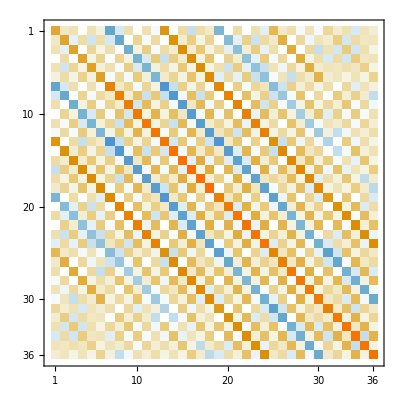

```mathematica
MatrixPlot[HND]
```

```mathematica
HD=DiagonalMatrix[Table[(0.5 π^2(basisIndexes[[k,1]]^2+basisIndexes[[k,2]]^2))/4,{k,1,Length[basisIndexes]}]];
```

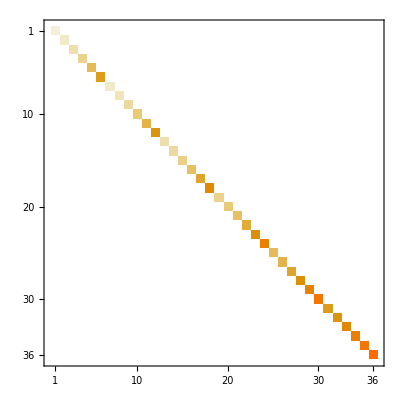

```mathematica
MatrixPlot[HD]
```

```mathematica
HM=HD+200000.HND;
NEV=Eigenvalues[HM];
EV=Sort[NEV];
Evec=Eigenvectors[HM][[Ordering[NEV]]];
```

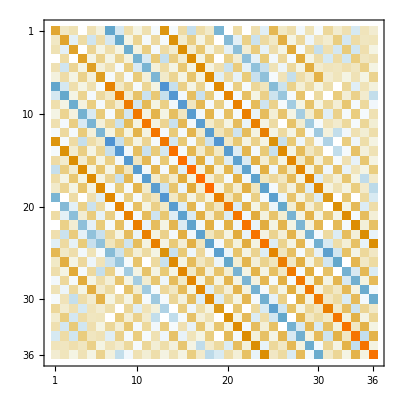

```mathematica
MatrixPlot[HM]
```

```mathematica
ϕSolution[x_,y_,nes_]:=Sum[
Evec[[nes,k]]*ϕm[x,y,basisIndexes[[k,1]],basisIndexes[[k,2]]],
{k,1,Length[basisIndexes]}
];
```

```mathematica
Manipulate[
DensityPlot[
ϕSolution[x,y,nes]^2,{x,0,2},{y,0,2},RegionFunction->Function[{x,y,z},Sqrt[(x-1)^2+(y-1)^2]<1&&x<1+cu],
AxesOrigin->{1,1},
ColorFunction->"Rainbow",
Mesh->Automatic,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->400,
FrameLabel->{Style["x",15], Style["y",15]},
PlotLegends->Automatic,
PlotRange->{{0,2},{0,2},All}
],
{nes,1,Length[Evec],1},
ContinuousAction->False,
SynchronousUpdating->False,
ControllerLinking->False
]
```

## Visualizar región

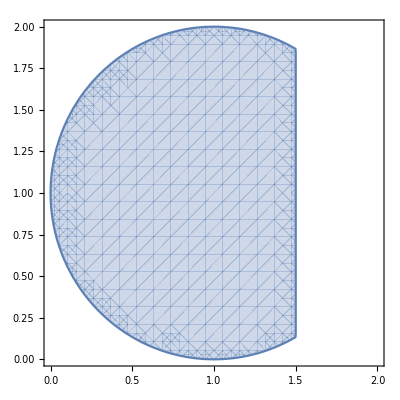

```mathematica
RegionPlot[(x-1)^2+(y-1)^2<1&&x<1+cu,{x,0,2},{y,0,2}]
```

## Eigenvalores de energía

```mathematica
EV
```

{5.92915,11.576,16.9423,22.0206,27.4379,33.9952,131.523,259.538,282.45,353.654,489.162,642.525,878.537,982.668,1163.41,2081.9,2332.17,2895.56,19759.,26433.8,31309.6,39328.8,74685.6,74826.,76299.9,79050.2,80602.9,85753.3,147276.,162153.,196956.,196972.,197032.,197098.,197500.,197666.}